```mathematica
pa={Flatten[Table[{"C"<>ToString[i],"E"<>ToString[i],"G"<>ToString[i]},{i,3,8}]],
Flatten[Table[{"A"<>ToString[i-1],"C"<>ToString[i],"E"<>ToString[i]},{i,3,8}]],
Flatten[Table[{"F"<>ToString[i-1],"A"<>ToString[i-1],"C"<>ToString[i]},{i,3,8}]],
Flatten[Table[{"G"<>ToString[i-1],"B"<>ToString[i-1],"D"<>ToString[i]},{i,3,8}]]};
pa=pa⟦All,1;;16⟧;
pa=Flatten[Table[{pa⟦i⟧,Reverse[pa⟦i⟧]},{i,1,4}]];
```

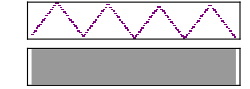

```mathematica
Sound[Flatten[
Table[SoundNote[pa⟦i⟧,{(i-1)/16,i/16},"Piano",SoundVolume->0.85],{i,1,Length[pa]}]
]]
```

```mathematica
c={
{"C3","C4","E4","G4","C5","E5","G5"},(*1^*)
{"A2","A3","C4","E4","A4","C5","E5"},(*6*)
{"F2","F3","A3","C4","F4","A4","C5"},(*4*)
{"G2","G3","B3","D4","G4","B4","D5"}    (*5*)
};
```

```mathematica
(*把音符一分为二*)
vol=0.7;
sl[array_,con_]:=If[con,
{SoundNote[array⟦1⟧,{array⟦2,1⟧,array⟦2,2⟧-1/4},array⟦3⟧,SoundVolume->vol],

SoundNote[array⟦1⟧,{array⟦2,1⟧+1/4,array⟦2,2⟧},array⟦3⟧,SoundVolume->vol]},
SoundNote[array⟦1⟧,array⟦2⟧,array⟦3⟧,SoundVolume->vol]
]
```

```mathematica
Accomp[no_,st_,slshli_,moveli_]:=Table[{
Table[SoundNote[c⟦n,1⟧,{8s+2(n-1),8s+2n},"Violin",SoundVolume->0.85],{n,1,4}],
Table[sl[{
(*转位*) If[MemberQ[moveli,m],c⟦n,3;;5⟧,c⟦n,1;;4⟧]
,{8s+2(n-1)+(m-1)/2,8s+2(n-1)+m/2},"Piano"},MemberQ[slshli,m]],{n,1,4},{m,1,4}]
},{s,no-1,no-1+st-1}]
```

```mathematica
cs={
{"G4","C5","E5","G5","C6","E6","G6"},(*1^*)
{"E4","A4","C5","E5","A5","C6","E6"},(*6*){"C4","F4","A4","C5","F5","A5","C6"},(*4*){"D4","G4","B4","D5","G5","B5","D6"}    (*5*)
};
```

```mathematica
Gen[num_,st_]:=(g=RealDigits[num,10,8*(st+1)]⟦1⟧;
mainli=Table[If[OddQ[s],g⟦8s-6;;8s-1⟧,g⟦8s-10;;8s⟧],{s,1,st}];(*奇偶小节疏密交错*)
slshli=Table[{Mod[g⟦no⟧,4,1]},{no,1,st}];
moveli=Table[Mod[g⟦no+1;;no+2⟧,4,1],{no,1,st}];
Sound[Flatten[{(*每两小节伴奏用不同节奏*)Table[Accomp[no,2,slshli⟦no⟧,moveli⟦no⟧],{no,1,st}],
Table[If[MemberQ[mainli⟦Ceiling[i/(8*4)]⟧,Mod[i,8,1]]||Mod[Ceiling[i/8],4]==3,(*主旋律的节奏表*)SoundNote[cs⟦Mod[Ceiling[i/8],4,1],
(*主旋律每小节用相同序列*) Mod[g⟦Mod[i,8,1]+Floor[i/32]*8⟧,6]+2⟧,{8+(i-1)/4,8+i/4},If[OddQ[Floor[i/32-0.01]],"Piano","Flute"]]],{i,1,32*(st-1)}],
(*点缀*) Table[SoundNote[pa⟦i⟧,{8st/2+(i-1)/16,8st/2+i/16},"Piano"],{i,1,Length[pa]}],
Table[SoundNote[pa⟦i⟧,{8st+(i-1)/16,8st+i/16},"Piano"],{i,1,Length[pa]}]
}]]
)
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["pi.mp3",Gen[π,8]]
Export["e.mp3",Gen[E,8]]
Export["sqrt2.mp3",Gen[√2,8]]
```

pi.mp3

e.mp3

sqrt2.mp3

```mathematica
Export["pi.mid",Gen[π,8]]
Export["e.mid",Gen[E,8]]
Export["sqrt2.mid",Gen[√2,8]]
```

pi.mid

e.mid

sqrt2.mid